```mathematica
(**)
```

```mathematica
mulMat[a_ , b_]:=Module[{all,aRows , aCols , bRows , bCols , cRows , cCols,currentC , currentA , currentB},
aRows = Dimensions[a][[1]];
aCols = Dimensions[a][[2]];
bRows = Dimensions[b][[1]];
bCols = Dimensions[b][[2]];
If[aCols≠ bRows , Throw["The number of columns in matrix a is not the same as the number of columns in matrix b"]];
cRows = aRows;
cCols = bCols;
currentC = Table["□" , {cRows} , {cCols}];
all = {Row[{MatrixForm[a] ,".", MatrixForm[b] , "=" , MatrixForm[currentC]}]};
Do[
Do[
Do[
currentA = 
Table[
If[
i==row&&j == k , 
Style[a[[i , j]] , {Bold,Red}] , 
Style[a[[i,j]] , Blue]] 
, {i , 1 , aRows} , {j , 1 , aCols}];
currentB = 
Table[
If[
i == k &&j==col , 
Style[b[[i , j]] , {Bold,Red}] , 
Style[b[[i,j]] , Blue]] 
, {i , 1 , bRows} , {j , 1 , bCols}];
currentC[[row , col]] = Sum[a[[row , i]] b[[i , col]] , {i , 1 , k}];
AppendTo[all , Row[{MatrixForm[currentA] ,".", MatrixForm[currentB] , "=" , MatrixForm[currentC]}]];
,{k , 1 , aCols}]
,{row , 1 , cRows}]
,{col , 1 , cCols}];
{all , a.b}
]
```

```mathematica
steps0 =mulMat[{{1 , 2 , 3}} , {{9 , 8 , 7} , {6 , 5 , 4} , {3 , 2 ,1}}];
```

```mathematica
Manipulate[steps0[[1]][[ii]] , {ii ,1 , Dimensions[steps0[[1]]][[1]] , 1}]
```

```mathematica
steps1 =mulMat[{{1 , 2 , 3},{4 , 5 , 6},{7 , 8 , 9}} , {{9 , 8 , 7} , {6 , 5 , 4} , {3 , 2 ,1}}];
```

```mathematica
Manipulate[steps1[[1]][[ii]] , {ii ,1 , Dimensions[steps1[[1]]][[1]] , 1}]
```

```mathematica
p::usage = "p[i] is the probability of finding the system in state i.";
```

```mathematica
state = {{p[1] , p[2] , p[3]}};
```

```mathematica
transition = Table[p[i->j] , {i , 1 , 3} , {j , 1 , 3}];
```

```mathematica
steps2 = mulMat[state , transition];
```

```mathematica
Manipulate[steps2[[1]][[ii]] , {ii ,1 , Dimensions[steps2[[1]]][[1]] , 1}]
```

```mathematica
steps3 = mulMat[transition , transition];
```

```mathematica
Manipulate[steps3[[1]][[ii]] , {ii ,1 , Dimensions[steps3[[1]]][[1]] , 1}]
```

```mathematica
(**)
```

```mathematica
tr::usage = "tr[a , b , p] represents a transition form state a to state b with probability p.";
```

```mathematica
transition = tr[_ , _ , _Real];
```

```mathematica
start[tr[a_ , b_ , p_Real]]:=a;
end[tr[a_ , b_ , p_Real]]:=b;
pr[tr[a_ , b_ , p_Real]]:= p;
```

```mathematica
getNodes[process:{transition...}]:=Union[Join[start/@process , end/@process]];
```

```mathematica
checkProcess[process:{transition...}]:=
Module[{nodes,checkEscape},
nodes = getNodes[process];
Do[
checkEscape = Total[pr/@Cases[process , tr[nodes[[ii]] , _ , _]]];
If[checkEscape ≠ 1, Throw["Total probability of escaping from node -"<>ToString[nodes[[ii]]]<>"- is not equal to 1.0"]]
,{ii , 1 , Dimensions[nodes][[1]]}];
]
```

```mathematica
makeGraph[process:{transition...}]:=Module[{checkEscape},
checkProcess[process];
Graph[Labeled[start[#] ->end[#] , pr[#]]&/@process,VertexLabels->"Name"]
];
```

```mathematica
getMatrix[process:{transition...} , OptionsPattern[{"rightMatrix"->False}]]:=
Module[{nodes , pm},
checkProcess[process];
nodes = getNodes[process];
pm = Table[
Total[pr/@Cases[process , tr[nodes[[ii]] , nodes[[jj]] , _Real]]]
,{ii , 1 , Dimensions[nodes][[1]]} , {jj , 1 , Dimensions[nodes][[1]]}];
If[OptionValue["rightMatrix"] , Transpose[pm],pm]
]
```

```mathematica
weather = {tr["Asunny" , "Brainy" , 0.1] , tr["Asunny" , "Asunny" , 0.9] , tr["Brainy" , "Asunny" , 0.5] , tr["Brainy" , "Brainy" , 0.5]};
```

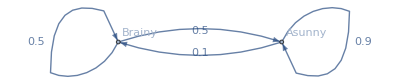

```mathematica
makeGraph[weather]
```

```mathematica
weatherMatrix = getMatrix[weather];
```

```mathematica
weatherMatrix//MatrixForm
```

(0.9 | 0.1
0.5 | 0.5)

```mathematica
weatherEigen = Eigensystem[Transpose[weatherMatrix]];
```

```mathematica
weatherEigen[[2,1]]/Total[weatherEigen[[2,1]]]
```

{0.833333,0.166667}

```mathematica
%.weatherMatrix
```

{0.833333,0.166667}

```mathematica
weatherEigen[[2,2]]
```

{-0.707107,0.707107}

```mathematica
stockMarket = {tr["bull" , "bull" , 0.9] , tr["bear" , "bear" , 0.8] , tr["stagnant" , "stagnant" , 0.5] , tr["bull" , "bear" , 0.075] , tr["bull" , "stagnant" , 0.025] , tr["bear" , "bull" , 0.15] , tr["bear" , "stagnant" , 0.05] , tr["stagnant" , "bull" , 0.25],tr["stagnant" , "bear" , 0.25]};
```

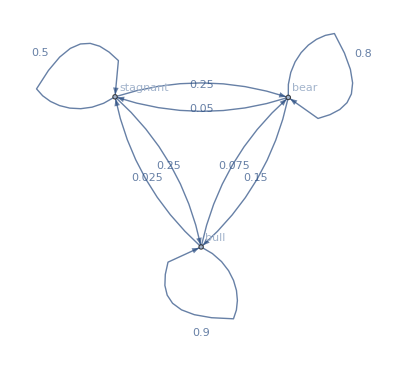

```mathematica
makeGraph[stockMarket]
```

```mathematica
stockMarket//getNodes
```

{bear,bull,stagnant}

```mathematica
stockMarketMatrix = getMatrix[stockMarket];
```

```mathematica
stockMarketMatrix//MatrixForm
```

(0.8 | 0.15 | 0.05
0.075 | 0.9 | 0.025
0.25 | 0.25 | 0.5)

```mathematica
stockMarketEigen = Eigensystem[stockMarketMatrix//Transpose];
```

```mathematica
station = stockMarketEigen[[2,1]]/Total[stockMarketEigen[[2,1]]]
```

{0.3125,0.625,0.0625}

```mathematica
station.stockMarketMatrix
```

{0.3125,0.625,0.0625}

```mathematica
stockMarketMatrix100 = MatrixPower[stockMarketMatrix , 100]
```

{{0.3125,0.625,0.0625},{0.3125,0.625,0.0625},{0.3125,0.625,0.0625}}

```mathematica
stockMarketMatrix100//MatrixForm
```

(0.3125 | 0.625 | 0.0625
0.3125 | 0.625 | 0.0625
0.3125 | 0.625 | 0.0625)

```mathematica
{0.1 ,0.8  ,0.1}.stockMarketMatrix100
```

{0.3125,0.625,0.0625}

```mathematica
getNodes[stockMarket]
```

{bear,bull,stagnant}

```mathematica
evolveState[n_ , initial_List][process:{transition...}]:=Module[{t , s , evolution},
t = getMatrix[process];
If[Dimensions[initial][[1]] ≠ Dimensions[t][[1]], Throw["Initial state size does not match probability matrix size."]];
s = initial / Total[initial];
evolution = NestList[#.t& , s , n];
Graphics[
{
Table[{GrayLevel[1.0-evolution[[ii , jj]]] , Disk[{jj , -ii} , 0.2]} , {ii , 1 ,Dimensions[evolution][[1]]} , {jj , 1 , Dimensions[evolution][[2]]}],
Table[Table[{GrayLevel[1.0-t[[jj , kk]]] , Arrow[{{jj , -ii} , {kk , -(ii+1)}}]} , {jj , 1 , Dimensions[evolution][[2]]} , {kk , 1 , Dimensions[evolution][[2]]}] , {ii , 1 ,Dimensions[evolution][[1]]-1}],
{Black,Text[#[[2]],{#[[1]] , -1+1}]&/@Partition[Riffle[Range[Dimensions[s][[1]]] , s],2]},
{Black,Text[#[[2]],{#[[1]] , -n-1-1}]&/@Partition[Riffle[Range[Dimensions[s][[1]]] , evolution[[-1]]],2]}
}
]
];
```

```mathematica
drawTrajectories[traj_]:=Module[{},
Table[Graphics[Line[Table[{traj[[ii]][[jj]],-jj} , {jj , 1 , Dimensions[traj[[ii]]][[1]]}]]] , {ii , 1 , Dimensions[traj][[1]]}]
];
```

```mathematica
generateTrajectories[n_ ,nt_, initial_List][process:{transition...}]:=Module[{t , s , evolution , all , repr , tab},
t = getMatrix[process];
If[Dimensions[initial][[1]] ≠ Dimensions[t][[1]], Throw["Initial state size does not match probability matrix size."]];
s = initial / Total[initial];
evolution = NestList[#.t& , s , n];
all = Table[RandomChoice[#-> Range[Dimensions[s][[1]]]]&/@evolution , {nt}];
tab=Table[Table[N[Count[all[[1;;tt , tm]] ,st]/tt] , {tm , 1 , Dimensions[evolution][[1]]} , {st , 1 , Dimensions[evolution][[2]]}] , {tt , 1 , nt}];
Table[ 
Graphics[
{
Table[{GrayLevel[1.0-tab[[tt]][[ii , jj]]] , Disk[{jj , -ii} , 0.2]} , {ii , 1 ,Dimensions[tab[[tt]]][[1]]} , {jj , 1 , Dimensions[tab[[tt]]][[2]]}],
{Black,Text[#[[2]],{#[[1]] , -1+1}]&/@Partition[Riffle[Range[Dimensions[s][[1]]] , s],2]},
{Black,Text[#[[2]],{#[[1]] , -n-1-1}]&/@Partition[Riffle[Range[Dimensions[s][[1]]] , tab[[tt]][[-1]]],2]},
{Red , Line[Table[{all[[tt]][[jj]],-jj} , {jj , 1 , Dimensions[all[[tt]]][[1]]}]]}
}
]
, {tt , 1 , nt}]
];
```

```mathematica
{0.3124999999999998,0.6250000000000001,0.06250000000000007}
```

{0.3125,0.625,0.0625}

```mathematica
getNodes[stockMarket]
```

{bear,bull,stagnant}

```mathematica
Manipulate[evolveState[8 , {pBear , pBull , pStagnant}][stockMarket] , {{pBear , 1} , 0 , 1} , {{pBull , 0} , 0 , 1} , {{pStagnant , 0} , 0 , 1}]
```

```mathematica
trajs = generateTrajectories[8 , 1000,{1 , 0 , 0}][stockMarket];
```

```mathematica
Manipulate[trajs[[ii]] , {ii , 1 , Dimensions[trajs][[1]] , 1}]
```

```mathematica
(*stockMarket = {tr["bull" , "bull" , 0.9] , tr["bear" , "bear" , 0.8] , tr["stagnant" , "stagnant" , 0.5] , tr["bull" , "bear" , 0.075] , tr["bull" , "stagnant" , 0.025] , tr["bear" , "bull" , 0.15] , tr["bear" , "stagnant" , 0.05] , tr["stagnant" , "bull" , 0.25],tr["stagnant" , "bear" , 0.25]};*)
```

```mathematica
(**)
```

```mathematica
makeGraph[stockMarket]
```

-Graphics-

```mathematica
pStockMarket = getMatrix[stockMarket];
```

```mathematica
pStockMarket//MatrixForm
```

(0.8 | 0.15 | 0.05
0.075 | 0.9 | 0.025
0.25 | 0.25 | 0.5)

```mathematica
Manipulate[MatrixPower[pStockMarket , n]//MatrixForm , {n , 1 , 100 , 1}]
```

```mathematica
esStockMarket = Eigensystem[Transpose[pStockMarket]]
```

{{1.,0.741421,0.458579},{{-0.445435,-0.890871,-0.0890871},{-0.673392,0.73658,-0.0631886},{-0.527733,-0.275692,0.803425}}}

```mathematica
esStockMarket[[2]][[1]]/Total[esStockMarket[[2]][[1]]]
```

{0.3125,0.625,0.0625}

```mathematica
%//Total
```

1.

```mathematica
example1 = {tr["0" , "0" , 1/2] , tr["1" , "1" , 1/4] , tr["0" , "1" , 1/2] , tr["1" , "0" , 3/4] , tr["2","2" , 1/2] , tr["2" , "1" , 1/4] , tr["2" , "3" , 1/4] , tr["3" , "3" , 1]}//N;
```

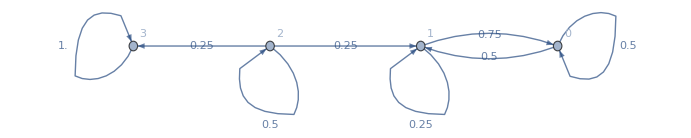

```mathematica
makeGraph[example1]
```

```mathematica
example1P=getMatrix[example1];
```

```mathematica
example1P//MatrixForm
```

(0.5 | 0.5 | 0 | 0
0.75 | 0.25 | 0 | 0
0 | 0.25 | 0.5 | 0.25
0 | 0 | 0 | 1.)

```mathematica
example1ES=Eigensystem[Transpose[example1P]]
```

{{1.,1.,0.5,-0.25},{{0.83205,0.5547,0.,0.},{0.,0.,0.,1.},{-0.408248,0.,0.816497,-0.408248},{-0.707107,0.707107,0.,0.}}}

```mathematica
st1 = example1ES[[2]][[1]]/Total[example1ES[[2]][[1]]]
```

{0.6,0.4,0.,0.}

```mathematica
st1.example1P
```

{0.6,0.4,0.,0.}

```mathematica
st2 = example1ES[[2]][[2]]/Total[example1ES[[2]][[2]]]
```

{0.,0.,0.,1.}

```mathematica
st2.example1P
```

{0.,0.,0.,1.}

```mathematica
Manipulate[MatrixPower[example1P , n]//MatrixForm , {n , 1 , 100 , 1}]
```

```mathematica
example2 = {tr["0" , "1" , 1.] , tr["1" , "0" , 1.]};
```

```mathematica
example2P = getMatrix[example2];
```

```mathematica
example2P//MatrixForm
```

(0 | 1.
1. | 0)

```mathematica
example2ES = Eigensystem[example2P];
```

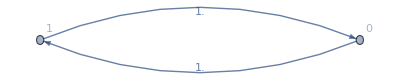

```mathematica
makeGraph[example2]
```

```mathematica
st=example2ES[[2,2]]/Total[example2ES[[2,2]]]
```

{0.5,0.5}

```mathematica
st.example2P
```

{0.5,0.5}

```mathematica
Manipulate[MatrixPower[example2P , n]//MatrixForm , {n , 1 , 100 , 1}]
```

```mathematica
example3 = {tr["0" , "1" , 1.] , tr["1" , "2" , 1.] , tr["2" , "3" , 1.],tr["3" , "4" , 1.],tr["4" , "0" , 1.]};
```

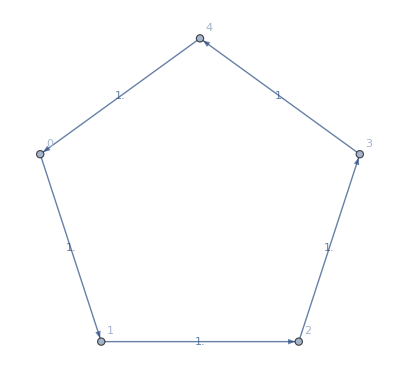

```mathematica
makeGraph[example3]
```

```mathematica
example3P = getMatrix[example3];
```

```mathematica
example3P//MatrixForm
```

(0 | 1. | 0 | 0 | 0
0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 1.
1. | 0 | 0 | 0 | 0)

```mathematica
Manipulate[MatrixPower[example3P , n]//MatrixForm , {n , 1 , 100 , 1}]
```

```mathematica
Manipulate[ListPlot[{Table[a/n^2 , {n , 1 , 10}] , Table[b Exp[-(n-3)^2] , {n , 1 , 10}]}] , {{a , 1} , 0 , 10} , {{b , 1} , 0 , 10}]
```